```mathematica
<<Units`
```

```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Mass m, kinetic energy ϵ incident on a target M

```mathematica
Solve[ReplaceAll[(γ-1)m==ϵ,γ->1/Sqrt[1-β^2]],β]
```

{{β→-(√ϵ √(2 m+ϵ))/(m+ϵ)},{β→(√ϵ √(2 m+ϵ))/(m+ϵ)}}

#### Rutherford cross section for energy loss Ed (classical, spin-0 and spin-1/2)

```mathematica
rutherford=(2Pi α^2 Z^2)/(M β^2 Ed^2);
```

```mathematica
rutherford0=(2Pi α^2 Z^2)/(M β^2 Ed^2)(1-β^2 Ed/ekin);
```

```mathematica
rutherford2=(2Pi α^2 Z^2)/(M β^2 Ed^2)(1-β^2 Ed/ekin+1/2(Ed/(ϵ+m))^2);
```

#### For simple rutherford cross section, stopping power is purely logarithmic in bounds

```mathematica
Integrate[rutherford*n*Ed,{Ed,emin,emax},Assumptions->{Ed>0,emin>0,emax>emin}]
```

(2 n π Z^2 α^2 Log[emax/emin])/(M β^2)

#### Scattering off Degenerate Targets, Fermi Energy Ef

```mathematica
npaulirel:=Integrate[e^2/Pi^2,{e,Ef-Ed,Ef}]
```

```mathematica
Convert[10^33 Centimeter^-3*(200 Mega ElectronVolt*Fermi)^3,(Mega ElectronVolt)^3]
```

8 ElectronVolt^3 Mega^3

```mathematica
ReplaceAll[npaulirel,Ed->Ef]
```

Ef^3/(3 π^2)

```mathematica
(3 Pi^2 n)^(1/3)/.n->8
```

2 3^(1/3) π^(2/3)

```mathematica
plotrel=Plot[ReplaceAll[npaulirel,{Ef->2 3^(1/3) π^(2/3),n->8}],{Ed,0,2 3^(1/3) π^(2/3)}];naiveplot=Plot[ReplaceAll[n*(Ed/Ef),{Ef->2 3^(1/3) π^(2/3),n->8}],{Ed,0,2 3^(1/3) π^(2/3)}];
```

#### Comparing “effective” number density available for depositing energy Ed with naive Pauli-blocking factor - upper end of plot is Ef.

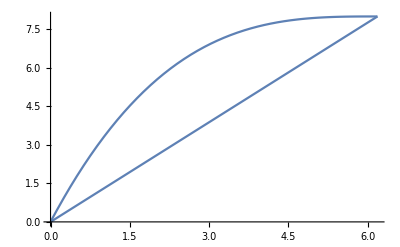

```mathematica
Show[plotrel,naiveplot]
```

#### Coulomb Log Emax

```mathematica
collision[b_]:=(2 Z^2 α^2)/(M b^2 β^2)
```

```mathematica
Ekin:=(2M β^2 γ^2)/(1+2γ (M/m)+(M/m)^2)
```

```mathematica
Equant:=collision[1/(Min[m,M]β*γ)]
```

#### Coulomb Log Emin

```mathematica
λTF=((6Pi Z α ne)/Ef)^(-1/2);
```

```mathematica
collision[1/me]
```

(2 me^2 Z^2 α^2)/(M β^2)

```mathematica
dedxpauli:=Integrate[dσdE*npaulirel*Ed,{Ed,(12 n π α^3)/(Ef me*β^2),emax}]/.{emax->maximum,Ef->(3 Pi^2 n)^(1/3)}/.{γ->1/Sqrt[1-β^2]}/.β->(√Eπ √(Eπ+2 mπ))/(Eπ+mπ)
```

#### Plots of R_ϵ due to Coulomb for different particles.

```mathematica
muoncoulomb=Table[{x/1000,Convert[(NIntegrate[dedxpauli^-1/.{M->0.511,me->0.511,α->1/137,mπ->100,Z->1,n->8},{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter]/Centimeter},{x,fSpace[500,10^9,100]}];
```

```mathematica
muoncoulombplot=Interpolation[muoncoulomb];
```

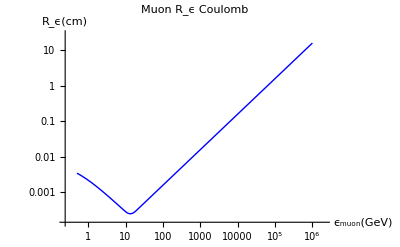

```mathematica
LogLogPlot[muoncoulombplot[x],{x,0.5,10^6},PlotStyle->{Thick,Blue},AxesLabel->{"ϵ_muon(GeV)","R_ϵ(cm)"},PlotLabel->"Muon R_ϵ Coulomb"]
```

#### Electrons

```mathematica
electroncoulomb=Table[{x/1000,Convert[(NIntegrate[dedxpauli^-1/.{M->0.511,me->0.511,α->1/137,mπ->0.511,Z->1,n->8},{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter]/Centimeter},{x,fSpace[10,10^9,100]}];
```

```mathematica
electroncoulombplot=Interpolation[electroncoulomb];
```

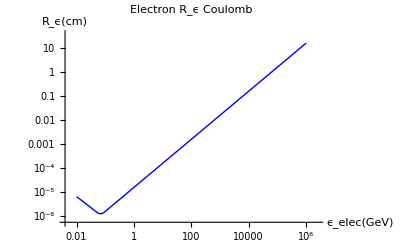

```mathematica
LogLogPlot[electroncoulombplot[x],{x,0.01,10^6},PlotStyle->{Thick,Blue},AxesLabel->{"ϵ_elec(GeV)","R_ϵ(cm)"},PlotLabel->"Electron R_ϵ Coulomb"]
```

#### Compare with nondegenerate stopping power.

```mathematica
Table[Convert[(NIntegrate[stoppingpower^-1/.{me->0.511,M->0.511,emin->10^-6,α->1/137,mπ->140,Z->1,n->8},{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{x,{10^2,10^3,10^4,10^5}}]
```

{8.02412×10^-9 Centimeter,1.12805×10^-7 Centimeter,9.32226×10^-7 Centimeter,8.02153×10^-6 Centimeter}

```mathematica
Table[Convert[(NIntegrate[stoppingpower^-1/.{me->0.511,M->0.511,emin->10^-6,α->1/137,mπ->0.5,Z->1,n->8},{Eπ,x/2,x}]/(Mega ElectronVolt))(200 Mega ElectronVolt*Fermi),Centimeter],{x,{10^2,10^3,10^4,10^5}}]
```

{1.11501×10^-8 Centimeter,9.82807×10^-8 Centimeter,8.78594×10^-7 Centimeter,7.94365×10^-6 Centimeter}